```mathematica
batchName="ReScaleRun 7-16-13"
```

ReScaleRun 7-16-13

```mathematica
SetDirectory["/home/trezitorul/Dropbox/SchoolYear12-13/UROP/Plasma Physics UROP/Code/LineSampling Scripts/Scripts/"<>batchName];
```

```mathematica
batchExpr=FileNames[]
```

{BdL,BdlHORTEST,dBdL,dn,dnB,n,ndB}

```mathematica
batchFiles=Map[Import,batchExpr]
```

{{BdL(6.08864, 1.132, 0, 181.701, 0.1)TI.curve,BdL(6.08864, 1.132, 0, 184.642, 0.1)TI.curve,BdL(6.08864, 1.132, 0, 187.853, 0.1)TI.curve,BdL(6.08864, 1.132, 0, 192.718, 0.1)TI.curve},{BdlHORTEST(6, 0, 0, 180, 0.1)TI.curve},{dBdL(6.08864, 1.132, 0, 181.701, 0.1)TI.curve,dBdL(6.08864, 1.132, 0, 184.642, 0.1)TI.curve,dBdL(6.08864, 1.132, 0, 187.853, 0.1)TI.curve,dBdL(6.08864, 1.132, 0, 192.718, 0.1)TI.curve},{dn(6.08864, 1.132, 0, 181.701, 0.1)TI.curve,dn(6.08864, 1.132, 0, 184.642, 0.1)TI.curve,dn(6.08864, 1.132, 0, 187.853, 0.1)TI.curve,dn(6.08864, 1.132, 0, 192.718, 0.1)TI.curve},{dnB(6.08864, 1.132, 0, 181.701, 0.1)TI.curve,dnB(6.08864, 1.132, 0, 184.642, 0.1)TI.curve,dnB(6.08864, 1.132, 0, 187.853, 0.1)TI.curve,dnB(6.08864, 1.132, 0, 192.718, 0.1)TI.curve},{n(6.08864, 1.132, 0, 181.701, 0.1)TI.curve,n(6.08864, 1.132, 0, 184.642, 0.1)TI.curve,n(6.08864, 1.132, 0, 187.853, 0.1)TI.curve,n(6.08864, 1.132, 0, 192.718, 0.1)TI.curve},{ndB(6.08864, 1.132, 0, 181.701, 0.1)TI.curve,ndB(6.08864, 1.132, 0, 184.642, 0.1)TI.curve,ndB(6.08864, 1.132, 0, 187.853, 0.1)TI.curve,ndB(6.08864, 1.132, 0, 192.718, 0.1)TI.curve}}

```mathematica
batchFiles=Table[Table[Directory[]<>"/"<>batchExpr[[i]]<>"/"<>batchFiles[[i]][[k]],{k,1,Length[batchFiles[[i]]]}],{i,1,Length[batchExpr]}];
```

```mathematica
batchData=Map[Import,batchFiles,{2}];
```

```mathematica
batchExpr
```

{BdL,BdlHORTEST,dBdL,dn,dnB,n,ndB}

```mathematica
batchExpr[[4]]
```

dn

```mathematica
batchFiles[[4]][[4]]
```

/home/trezitorul/Dropbox/SchoolYear12-13/UROP/Plasma Physics UROP/Code/LineSampling Scripts/Scripts/ReScaleRun 7-16-13/dn/dn(6.08864, 1.132, 0, 192.718, 0.1)TI.curve

```mathematica
Min[Table[batchData[[4]][[4]][[i]][[2]],{i,1,Length[batchData[[4]][[4]]]}]]
```

Min[-0.00141315,curve]

```mathematica
-0.001413148478604853/6.2416
```

-0.000226408

```mathematica
.0019527/6.2416
```

0.000312852

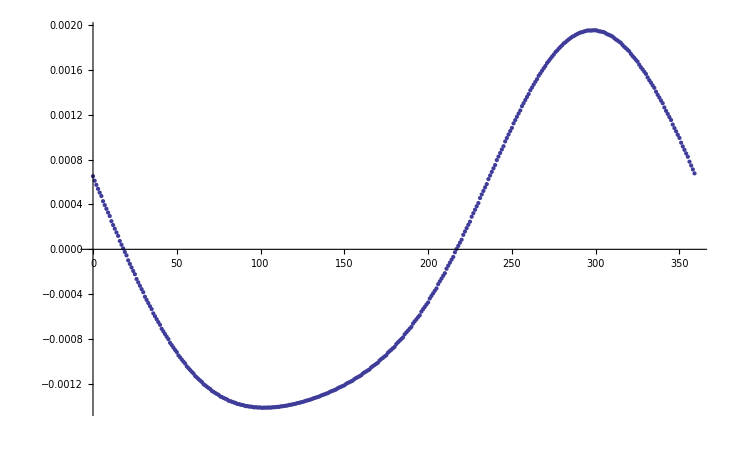

```mathematica
ListPlot[batchData[[4]][[4]]]
```

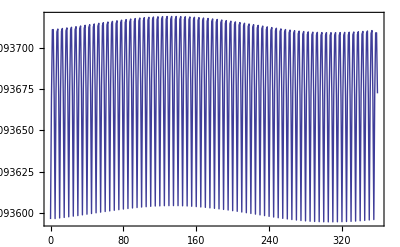
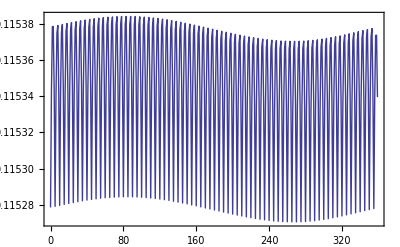
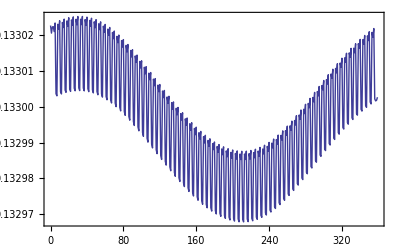
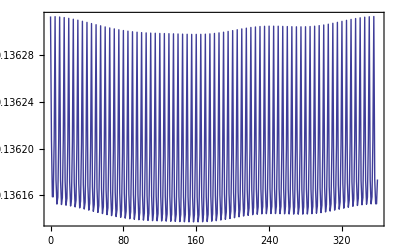
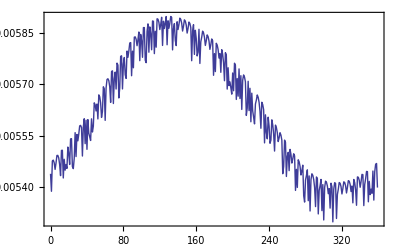
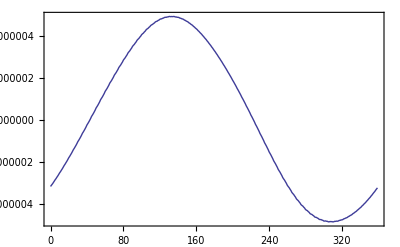
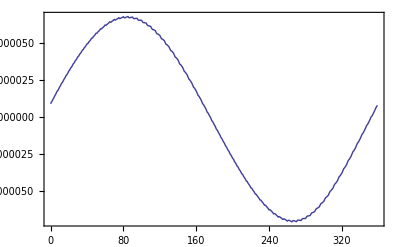
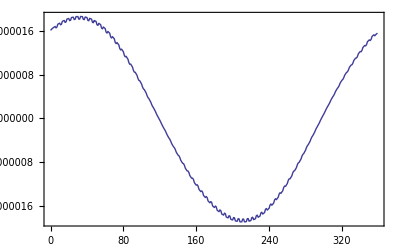

```mathematica
batchPlots=Map[ListPlot[#,Joined->True,Frame->True]&, batchData,{2}]
```

```mathematica
plotCol=Table[Table[{batchPlots[[j]][[i]]},{i,1,Length[batchPlots[[j]]]}],{j,1,Length[batchPlots]}];
```

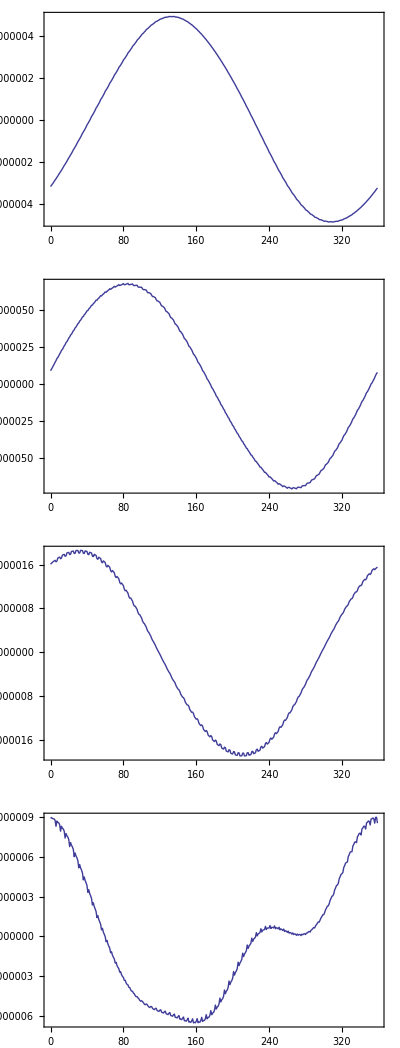

ReScaleRun 7-16-13<>dBdL

```mathematica
plot=3;
gridPlot=GraphicsGrid[plotCol[[plot]],Frame->All,PlotLabel-> batchExpr[[plot]]]
Export[batchName<>"<>"<>batchExpr[[plot]],gridPlot,"PDF", ImageSize-> {850,1100}]
```

```mathematica
batchExpr
```

{BdL,BdlHORTEST,dBdL,dn,dnB,n,ndB}

```mathematica
totalData=batchData[[5]]+batchData[[7]];
```

```mathematica
totalData= Table[Table[{totalData[[j]][[i]][[1]]/2,totalData[[j]][[i]][[2]]},{i,Length[totalData[[j]]]}],{j,1,Length[totalData]}];
```

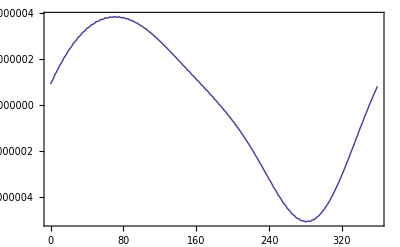
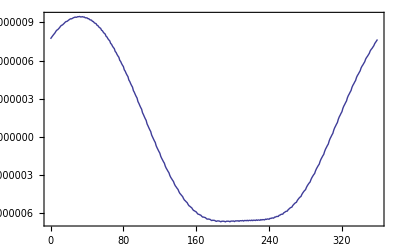
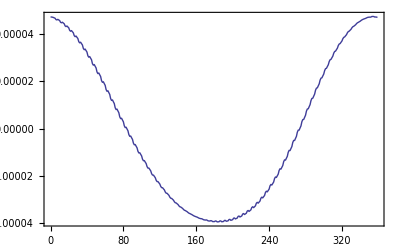
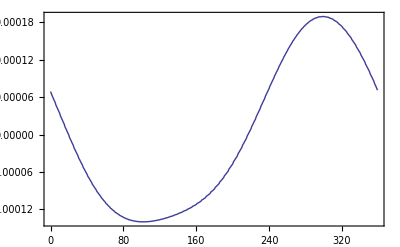

```mathematica
totalPlots=Map[ListPlot[#,Joined->True,Frame->True]&,totalData]
```

```mathematica
totalCol= Map[{#}&,totalPlots]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

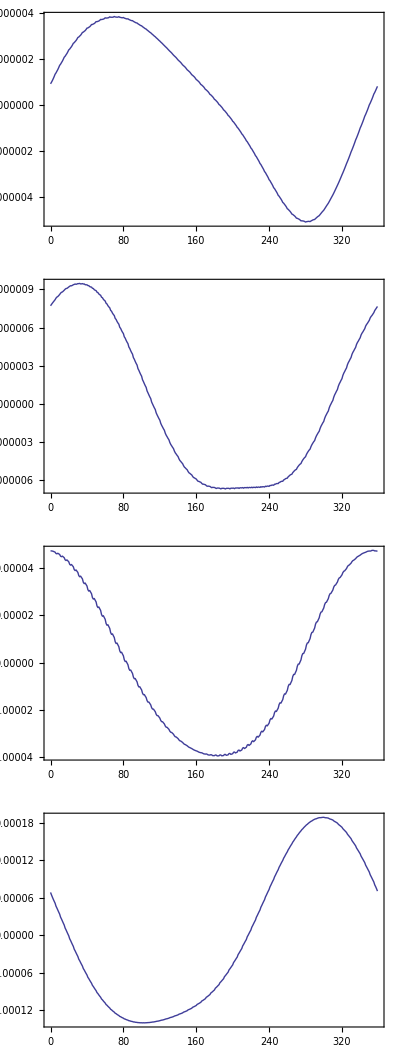

ReScaleRun 7-16-13<>Total Sum

```mathematica
totalGridPlot=GraphicsGrid[totalCol, PlotLabel-> "∫dnBdl + ∫dBndl", Frame->All]
Export[batchName<>"<>"<>"Total Sum",totalGridPlot,"PDF", ImageSize-> {850,1100}]
```